```mathematica
Clear[xStep];
xStep[n_] :=0 /; n≤0;
xStep[n_]:= 1 /; n>0;
```

```mathematica
Clear[yStep];
yStep[n_]:= yStep[n]= 0.098 xStep[n]+0.195 xStep[n-1]+0.098 xStep[n-2]+0.942 yStep[n-1]-0.333 yStep[n-2];
yStep[-1]= yStep[0]=0
```

0

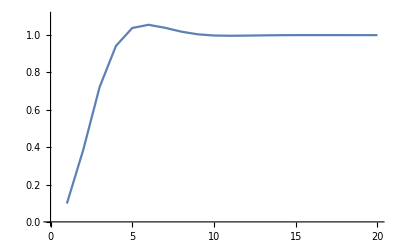

```mathematica
ListPlot[  Table[yStep[n],{n,20}],PlotRange -> {0.0,1.1}, Joined-> True]
```

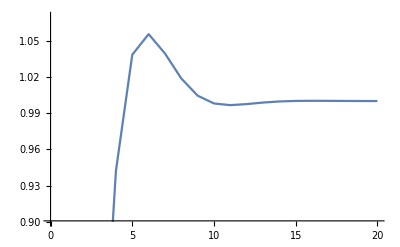

```mathematica
ListPlot[  Table[yStep[n],{n,20}],PlotRange -> {0.90,1.07}, Joined->True]
```

Explanation of xSine. A sine wave with frequency f can be described by the function sin(2π f t), where t is the time in seconds. If we sample this function with a sampling rate s (s times per second), we can discretize the time as t = n/s, where n=0,1,2, … is an integer representing the index of the sample. If the sampling rate is s=8000 Hz, n=8000 corresponds to the time 1 second. In the definition below s is written as samplingRate.

```mathematica
Clear[xSine];
samplingRate=8000.;  (* This is how often the signal is sampled. Do not change! *)
xSine[freq_,n_] := Sin[2 Pi  freq  n/samplingRate];
```

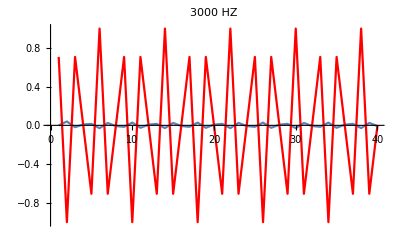

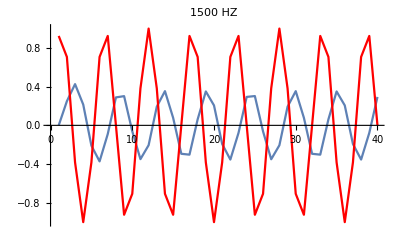

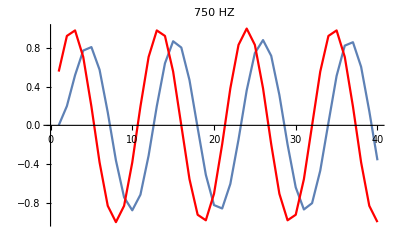

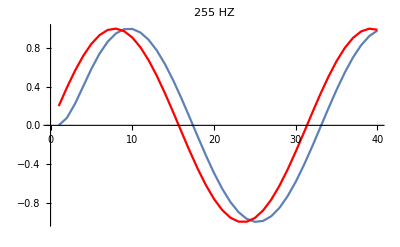

```mathematica
xFreq:=3000;
yFreq:=xFreq;

xList=ListPlot[  Table[xSine[xFreq,n],{n,40}],Joined->True, PlotStyle->Red];
Clear[y];
y[freq_,t_]:= y[t]= 
0.098 xSine[freq,t]+
0.195 xSine[freq,t-1]+
0.098 xSine[freq,t-2]+
0.942 y[t-1]-
0.333 y[t-2];

y[0]= y[-1]=0;
yList=ListPlot[  Table[y[yFreq,n],{n,40}],PlotRange->{-1,1}, Joined->True, PlotLabel->xFreq"HZ"];

Show[
yList,
xList](*xSine is red*)
```